2 ； Null

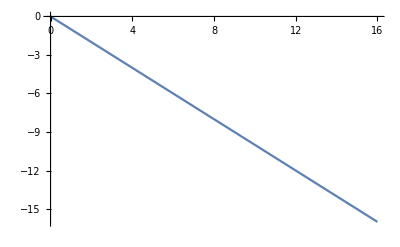

```mathematica
m1=3;m2=5;g=9.83;d=2；
δt=2.0×10^-3;n=8×10^3;
data={{0,0}};
v1data={{0,0}};
y1data={{0,0}};
v1=-1;
Do[
y1=y1data[[-1,2]]+δt v1;
AppendTo[y1data,{i δt,y1}],
{i,n}]
yy1[t_]:=Chop[Interpolation[y1data,t]];
Plot[yy1[t],{t,0,16}]
Manipulate[
Graphics[{Red,Disk[{0,yy1[i δtt]},0.5]}],
{i,1,n,1}]
Clear["Global`*"]
```